```mathematica
gr7[n_]:=Block[
{edges={1<-> 2,2<->3,3<->4,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10,6<->7,7<->8,8<->9,9<->5,9<->10,2<->6,1<->10,3<->7,8<->4,6<->10},i,previous=4},
For[i=11,i≤n,i++,
AppendTo[edges,previous<->i];
AppendTo[edges,i<->9];
previous=i
];
AppendTo[edges,previous<->5];
Graph[edges, GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
]
```

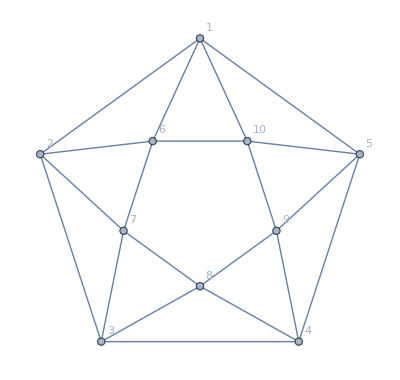

```mathematica
gr7[10]
```

```mathematica
EmbedGraph[graph_,vertexSets_]:=Block[{base=gr7[10],reference={1,2,3,4,5},g},
base=EdgeDelete[base,{1<->5,5<->4,4<->3,3<->2,2<->1}];
g=base;
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,vertexSets}];
Table[
g=EdgeAdd[g,{reference[[First[vertexSets[[e[[1]]]]]]]<->reference[[First[vertexSets[[e[[2]]]]]]]}],{e,EdgeList[graph]}];
Graph[EdgeList[g],GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
]
```

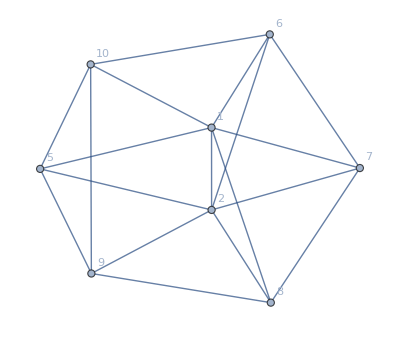

```mathematica
With[{g=EmbedGraph[allGraphs[alfa1Key,"graph"],allGraphs[alfa1Key,"vertexsets"]]},
g]
```

```mathematica
Labeled[Graph[DualGraph[Faces[g]],VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding"],Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]]]
```

```mathematica
Table[
With[{g=EmbedGraph[allGraphs[k,"graph"],allGraphs[k,"vertexsets"]]},
{VertexCount[g],EdgeCount[g],Length[Faces[g]],EdgeCount[DualGraph[Faces[g]]],VertexCount[DualGraph[Faces[g]]]}
],{k,{0}}]
```

{{10,15,6,10,7}}

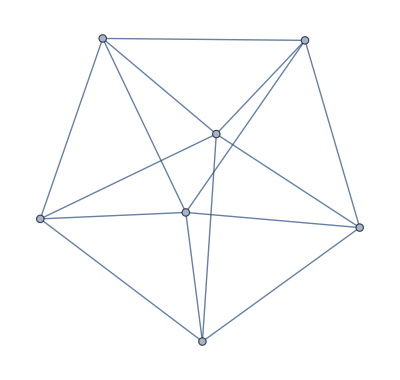

```mathematica
JacobsThalGraph2[7]
```

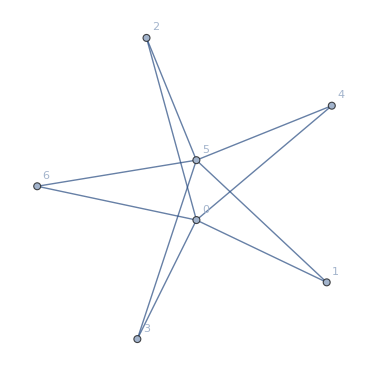
```mathematica
IsomorphicGraphQ[-Graphics-,JacobsThalGraph2[7]]
```

False